# MSBRDF for LTC Area Lights

We try and load the “roughness only” LTC tables generated by the LTC generator with a light-dependent MSBRDF term:

	L(ω_o)=∫_Ω L(ω_i)  f_ms( ω_o,ω_i,α) (ω_i · n) ⅆ ω_i
	L(ω_o)=∫_Ω L(ω_i)  ((1-E(ω_o,α))(1-E(ω_i,α)))/(π-E_avg(α)) (ω_i · n) ⅆ ω_i
	L(ω_o)=(1-E(ω_o,α))/(π-E_avg(α))∫_Ω L(ω_i)  (1-E(ω_i,α) (ω_i · n) ⅆ ω_i
	L(ω_o)=L_i ·(1-E(ω_o,α))/(π-E_avg(α))∫_Ω (1-E(ω_i,α) (ω_i · n) ⅆ ω_i
	L(ω_o)≃L̃(ω_o)=L_i ·(1-E(ω_o,α))/(π-E_avg(α))∫_Ω D(ω_i,α) ⅆ ω_i
	L̃(ω_o)=L_i ·(1-E(ω_o,α))/(π-E_avg(α))∫_Ω_0 D_0(ω_0,α) ⅆ ω_0

Here, D_0(ω_0,α) represents the clamped cosine distribution and Ω_0 the transformed solid angle.
Since the MSBRDF is very low-frequency and isotropic due to the fact it only depends on the light direction and roughne, the resulting transform matrix Ω_0 = M^-1 Ω is very sparse and contains only diagonal terms:

	M^-1 =(1 | 0 | 0
0 | 1 | 0
0 | 0 | m_33(α))

The idea is to read back the m_33 and magnitude values for each roughness and either export it to a CSV table or find a simple fitting...

## LTC Tables Loading

The roughness-only LTC tables have been exported as raw double values vectors { roughness, magnitude, m00, m20, m02, m22 }

```mathematica
LoadLTC=Function[{filename},
s=OpenRead[filename,BinaryFormat->True];
count=BinaryRead[s,"Integer32"];

temp=Table[BinaryRead[s,{ 
 "Real64"
, "Real64"
, "Real64", "Real64", "Real64", "Real64"}
],{i,1,count}];

Close[s];
l=Length[temp];
temp
];
```

```mathematica
ltcGGX=LoadLTC["D:\\Workspaces\\GodComplex\\Tools\\LTCTableGenerator\\MS_GGX.double"];
ltcOren=LoadLTC["D:\\Workspaces\\GodComplex\\Tools\\LTCTableGenerator\\MS_OrenNayar.double"];
```

### Remap into nice tables

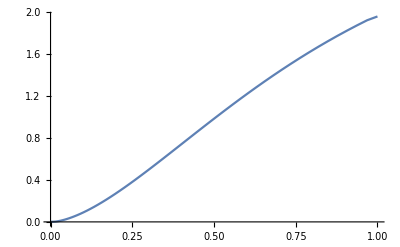

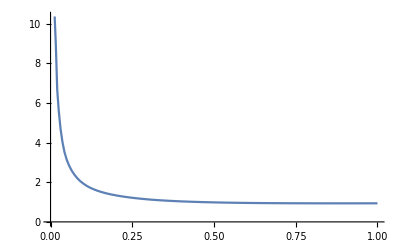

```mathematica
count=Length[ltcGGX];
(*taGGXmag=Table[{ (i-1)/(count-1), ltcGGX[[i]][[2]] }, {i,1,count}];
taGGXm33=Table[{ (i-1)/(count-1), ltcGGX[[i]][[6]] }, {i,1,count}];*)
taGGXm33=Table[{ ltcGGX[[i]][[1]], ltcGGX[[i]][[6]] }, {i,1,count}];
taGGXmag=Table[{ ltcGGX[[i]][[1]], ltcGGX[[i]][[2]] }, {i,1,count}];
taGGX=Table[{ ltcGGX[[i]][[1]] , ltcGGX[[i]][[6]], ltcGGX[[i]][[2]]}, {i,1,count}];
ListLinePlot[taGGXmag]
ListLinePlot[taGGXm33]
```

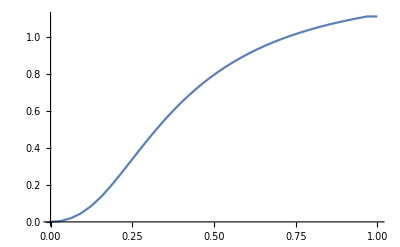

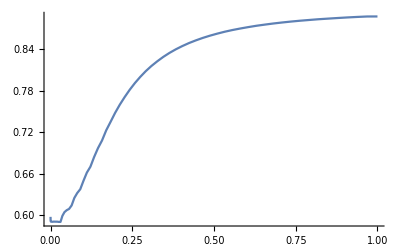

```mathematica
count=Length[ltcOren];
(*taOrenmag=Table[{ (i-1)/(count-1), ltcOren[[i]][[2]] }, {i,1,count}];
taOrenm33=Table[{ (i-1)/(count-1), ltcOren[[i]][[6]] }, {i,1,count}];*)
taOrenm33=Table[{ ltcOren[[i]][[1]], ltcOren[[i]][[6]] }, {i,1,count}];
taOrenmag=Table[{ ltcOren[[i]][[1]], ltcOren[[i]][[2]] }, {i,1,count}];
taOren=Table[{ ltcOren[[i]][[1]], ltcOren[[i]][[6]], ltcOren[[i]][[2]] }, {i,1,count}];
ListLinePlot[taOrenmag]
ListLinePlot[taOrenm33]
```

## Exporting Nice Tables as CSV for the blog

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
Export["MSLTC_GGX_64.csv", taGGX,"CSV"]
Export["MSLTC_Orennayar_64.csv", taOren,"CSV"]
```

MSLTC_GGX_64.csv

MSLTC_Orennayar_64.csv

## Attempt Fitting

### Remap into “perceptual roughness” tables

Here, the roughness varies linearly and is called the “perceptual roughness”  α'=√α

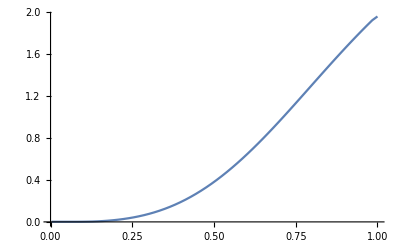

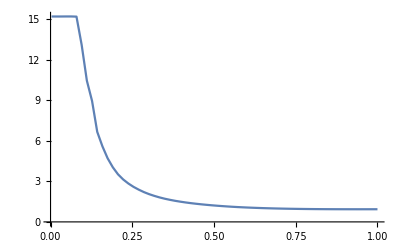

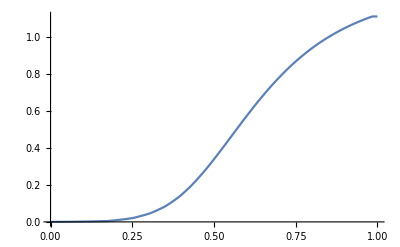

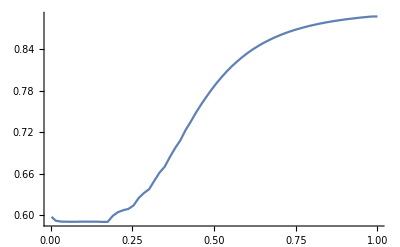

```mathematica
count=Length[ltcGGX];
taGGXm33=Table[{ (i-1)/(count-1), ltcGGX[[i]][[6]] }, {i,1,count}];
taGGXmag=Table[{ (i-1)/(count-1), ltcGGX[[i]][[2]] }, {i,1,count}];
taOrenm33=Table[{ (i-1)/(count-1), ltcOren[[i]][[6]] }, {i,1,count}];
taOrenmag=Table[{ (i-1)/(count-1), ltcOren[[i]][[2]] }, {i,1,count}];

taGGXm33=Table[{ √(ltcGGX[[i]][[1]]), ltcGGX[[i]][[6]] }, {i,1,count}];
taGGXmag=Table[{ √(ltcGGX[[i]][[1]]), ltcGGX[[i]][[2]] }, {i,1,count}];
taOrenm33=Table[{ √(ltcOren[[i]][[1]]), ltcOren[[i]][[6]] }, {i,1,count}];
taOrenmag=Table[{ √(ltcOren[[i]][[1]]), ltcOren[[i]][[2]] }, {i,1,count}];

ListLinePlot[taGGXmag]
ListLinePlot[taGGXm33,PlotRange->Full]
ListLinePlot[taOrenmag]
ListLinePlot[taOrenm33]
```

```mathematica
fittingMethod="Automatic";
```

{a→0.,b→0.0979143,c→-1.42729,d→7.76823,e→-4.47564}

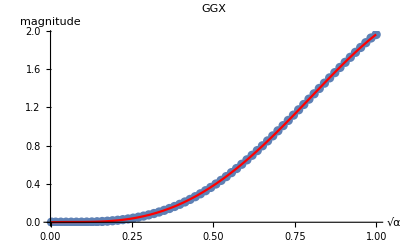

```mathematica
model=0*a+b*x+c*x^2+d*x^3+e*x^4;
data=taGGXmag;
fit=FindFit[data,model,{{a,1},{b,1},{c,1},{d,0},e},x,Method->fittingMethod]
fGGXmag=Function[{x},Evaluate[model/.fit]];
Show[
ListPlot[data,PlotRange->Full,PlotLabel->"GGX",AxesLabel->{"√α","magnitude"}]
,Plot[fGGXmag[x],{x,0,1},PlotStyle->Red,PlotRange->Full]
]
```

```mathematica
a->0.,b->0.09791431592022058,c->-1.4272852958071647,d->7.768226052923069,e->-4.475643330561517}
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {4.81707×10^-12, 0.00092362, 4.86573×10^-12}, is returned.

{a→0.255902,b→-2.79445,c→8.29851,d→-4.66222,e→0.001,f→0.001}

Function[{x},0.255902-2.79445 x+8.29851 x^2-4.66222 x^3]

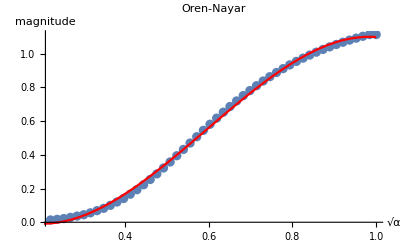

```mathematica
model=a+b*x+c*x^2+d*x^3+0*e*x^4+0*f*x^5;
data=Take[taOrenmag,-50];
fit=FindFit[data,{model,{c>0}},{{a,1},{b,1},{c,1},{d,0},e,f},x,Method->fittingMethod]
fOrenmag=Function[{x},Evaluate[model/.fit]]
Show[
ListPlot[data,PlotRange->Full,PlotLabel->"Oren-Nayar",AxesLabel->{"√α","magnitude"}]
,Plot[fOrenmag[x],{x,0,1},PlotStyle->Red,PlotRange->Full]
]
```

```mathematica
{a->0.2559021427001363,b->-2.7944531451217687,c->8.298513748611509,d->-4.662218902663712,e->0.001,f->0.001}
```

{a→21.3429,b→1.,c→93.0162,d→0.481472,e→1.,f→143.397}

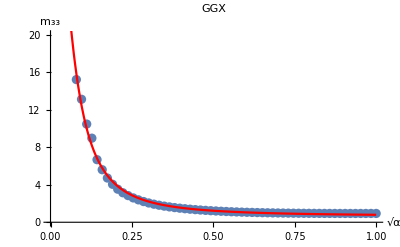

{0.00316228,15.2119}

```mathematica
model=(a+0*b*x+1*c*x^2)/(d+0*e*x+f*x^2);
data=Take[taGGXm33,-59];
fit=FindFit[data,model,{{a,1},{b,1},{c,1},{d,0},e,f},x,Method->fittingMethod]
fGGXm33=Function[{x},Evaluate[model/.fit]];
Show[
ListPlot[data,PlotRange->{{0,1},{0,20}},PlotLabel->"GGX",AxesLabel->{"√α","m_33"}]
,Plot[fGGXm33[x],{x,0,1},PlotStyle->Red,PlotRange->Full]
]
taGGXm33[[1]]
```

```mathematica
{a->21.342911007109528,b->1.,c->93.01620773161568,d->0.4814723396401988,e->1.,f->143.39682026031764}
```

{a→0.0050484,b→-0.0149282,c→0.0279305,d→0.00842088,e→-0.02235,f→0.0343437}

Function[{x},(0.0050484-0.0149282 x+0.0279305 x^2)/(0.00842088-0.02235 x+0.0343437 x^2)]

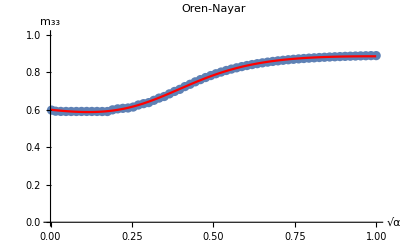

```mathematica
model=(a+b*x+c*x^2)/(d+e*x+f*x^2);
data=taOrenm33;
fit=FindFit[data,model,{{a,1},{b,1},{c,1},{d,0},e,f},x,Method->fittingMethod]
fOrenm33=Function[{x},Evaluate[model/.fit]]
Show[
ListPlot[data,PlotRange->{{0,1},{0,1}},PlotLabel->"Oren-Nayar",AxesLabel->{"√α","m_33"}]
,Plot[fOrenm33[x],{x,0,1},PlotStyle->Red]
]
```

```mathematica
Function[{x},(0.005048402287040277-0.014928238738260345 x+0.027930492034822143 x^2)/(0.008420878564907999-0.022349996757079705 x+0.034343673853208634 x^2)]
```